```mathematica
(* notebook to find energy density of stringbit *)
```

```mathematica
ClearAll[LoadEigenEnergies,LoadAndBucketEnergies,PlotEnergyBuckets];
DataFolder = NotebookDirectory[]<>"../data/";
Format[energy,StandardForm]="E";

(*Bucketed = 1 means already bucketed (default)
Bucketed = 0 means not yet
Bucketed > 1=n mean not yet and require split the data into n buckets.
*)
Options[LoadEigenEnergies]={Folder->DataFolder,Bucketed->1,  Single->False,ColorN->Infinity};
LoadEigenEnergies[s_,M_,opts:OptionsPattern[]]:=Module[{file,data},
file = "EEs="<> ToString[s] <> "M="<>ToString[M];
If[OptionValue[ColorN]≠Infinity, file = file <> "N="<>ToString[OptionValue[ColorN]]];
If[OptionValue[Single], file = file <>"s"];
If[OptionValue[Bucketed]==1, file = file <>"g"];
data = Import[OptionValue[Folder]<> file <> ".txt", "Table"];
If[OptionValue[Bucketed]≠1,data=Flatten[data]];
If[OptionValue[Bucketed]>1,data=BucketData[data,OptionValue[Bucketed]]];
If[OptionValue[Bucketed]≠0,data = RebucketData[data]];

Return[data];
];

ClearAll[BucketData];
BucketData[list_,n_]:=Module[{min,max,delta,res,pos,i},
min = First[list];
max=Last[list];
delta = (max-min)/n;
res = Table[{i*delta + min,0},{i,0,n}];

For[i=1,i≤Length[list],i++,
pos =Floor[(list[[i]]-min)/delta + 1.5];
res[[pos,2]]=res[[pos,2]]+1;
];

Return[res]
];

(*re-do the bucket. Merge buckets with zero data with their neibough*)
ClearAll[RebucketData]
RebucketData[data_]:=Module[{i,j,res={},lastZ=-1,ave,ret={}},
For[i=1,i≤Length[data],i++,
If[data[[i,2]]==0 && lastZ==-1,lastZ=i];

If[data[[i,2]]≠ 0,
If[lastZ>0,
ave=Sum[data[[j,1]],{j,lastZ,i-1}]/(i-lastZ);
AppendTo[res,{ave,0}];
lastZ=-1;
];

AppendTo[res, data[[i]]];
];
];

If[lastZ≠-1,
ave=Sum[data[[j,1]],{j,lastZ,Length[data]}]/(Length[data]-lastZ+1);
AppendTo[res,{ave,0}];
];
(*For[i=1,i≤ Length[res],i++,
If[res[[i,2]]==0 && i>1 && i <Length[res],
ret[[-1,1]]=(Last[ret][[1]]+res[[i,1]])/2;
AppendTo[ret,{ (res[[i,1]]+res[[i+1,1]])/2,res[[i+1,2]]}];
i=i+1,
AppendTo[ret,res[[i]]]
];
];

Print["tot3=",Sum[ret[[i]],{i,Length[ret]}]];*)

Return[res]
];

ClearAll[LoadThermalData];
Options[LoadThermalData]={Folder->DataFolder};
LoadThermalData[s_,M_,T0_,opts:OptionsPattern[]]:=Module[{file,data},
file = "THs="<> ToString[s] <> "M="<>ToString[M]<>"T0="<>ToString[T0];
data = Import[OptionValue[Folder]<> file <> ".txt", "Table"];
Return[data];
];

Options[LoadFluctuation]={Folder->DataFolder};
LoadFluctuation[s_,M_,opts:OptionsPattern[]]:=Module[{file,data},
file = "FLs="<> ToString[s] <> "M="<>ToString[M];
data = Import[OptionValue[Folder]<> file <> ".txt", "Table"];
Return[data];
];

MaxEnergy[s_,M_]:=4*s*Cot[Pi/(2*M)];
MinEnergy[s_,M_]:=If[Mod[M,2]==1,
-4*s*Cot[Pi/(2*M)],
If[Mod[M,4]==2,-8*Cot[Pi/M],-4*(Cot[Pi/(M-2)]+Cot[Pi/M+2])]
];

AveEnergyByZ[s_,M_,T0_,beta_]:=-T0^2*beta*SigmaFit[M]^2+1/Sqrt[2]*(M+T0*MuFit[M])-(Erf[(MaxEnergy[s,M]-MuFit[M])/(Sqrt[2]SigmaFit[M])+T0*beta*SigmaFit[M]/2]+Erf[(MuFit[M]-MinEnergy[s,M])/(Sqrt[2]SigmaFit[M])-T0*beta*SigmaFit[M]/2])^(-1)*1/Sqrt[Pi]*T0*SigmaFit[M]*(Exp[-((MaxEnergy[s,M]-MuFit[M])/(Sqrt[2]SigmaFit[M])+T0*beta*SigmaFit[M]/2)^2]-Exp[-((MuFit[M]-MinEnergy[s,M])/(Sqrt[2]SigmaFit[M])-T0*beta*SigmaFit[M]/2)^2]);

LogZ[s_,M_,T0_,beta_]:=1/2*T0^2*beta^2*SigmaFit[M]^2-1/Sqrt[2]*beta*(M+T0*MuFit[M])+(M-1)*Log[2]+Log[0.7261768]+Log[Erf[(MaxEnergy[s,M]-MuFit[M])/(Sqrt[2]SigmaFit[M])+T0*beta*SigmaFit[M]/2]+Erf[(MuFit[M]-MinEnergy[s,M])/(Sqrt[2]SigmaFit[M])-T0*beta*SigmaFit[M]/2]];

ClearAll[PlotThermalData];
PlotThermalData[s_,M_,T0_,maxB_:0]:=Module[
{data,Zdata,Edata,Sdata,ESdata,p1,p2,p3,p4,p1a,p2a,alpha=0.7261768,maxBeta},
data = LoadThermalData[s,M,T0];
Zdata = Table[{data[[i, 1]],data[[i,2]]},{i,1,Length[data]}];
Edata = Table[{data[[i, 1]],data[[i,3]]},{i,1,Length[data]}];
Sdata = Table[{data[[i, 1]],data[[i,4]]},{i,1,Length[data]}];
ESdata = Table[{data[[i, 3]],data[[i,4]]},{i,1,Length[data]}];
If[maxB>0,maxBeta=maxB,maxBeta = Last[data][[1]]];

p1=ListPlot[Zdata,AxesLabel->{"β", "ln(Z)"},PlotRange->{{0,maxBeta},{10,20}}];
p1a=Plot[LogZ[s,M,T0,beta],{beta,0,maxBeta}];
p2=ListPlot[Edata,AxesLabel->{"β", "E"},PlotRange->{{0,maxBeta},{-20,20}}];
p2a=Plot[AveEnergyByZ[s,M,T0,beta],{beta,0,maxBeta}];
p3=ListPlot[Sdata,AxesLabel->{"β", "S"}];
p4=ListPlot[ESdata,AxesLabel->{"E", "S"}];
Return[{{p1,p1a},{p2,p2a},{p3},{p4}}]
]

PlotFluctuation[s_,M_]:=Module[{data2,data,Z2},
data = LoadFluctuation[s,M];
Z2 = data[[1,2]]^2;
data2 = Table[{data[[i, 1]],(data[[i,2]]^2+data[[i,3]]^2)/Z2},{i,2,Length[data]}];
Return[ListPlot[data2]]
]

ClearAll[AverageEnergy];
Options[AverageEnergy]=Join[Options[LoadEigenEnergies],{}];
AverageEnergy[s_,M_, opts:OptionsPattern[]]:=Module[{data,data2,i,tot,count},
data = LoadEigenEnergies[s,M,FilterRules[{opts},Options[LoadEigenEnergies]]];
If[OptionValue[Bucketed]==0,
Return[Mean[data]],
tot=0;count=0;
For[i=1,i≤Length[data],i++,
tot += data[[i,1]] * data[[i,2]];
count += data[[i,2]]
];
Return[tot/count]
];
];

ClearAll[EnergyVariance];
Options[EnergyVariance]=Join[Options[LoadEigenEnergies],{}];
EnergyVariance[s_,M_, opts:OptionsPattern[]]:=Module[{data,data2},
data = LoadEigenEnergies[s,M,FilterRules[{opts},Options[LoadEigenEnergies]]];
data2=Table[data[[i]]^2,{i,1,Length[data]}];
Return[Mean[data2]-Mean[data]^2];
];

LoadAndBucketEnergies[s_,M_,n_]:=Module[{data,maxE,delta, buckets,i,pos},
data=LoadEigenEnergies[s,M];
maxE=N[4*s*Cot[Pi/(2M)]];
delta=2*maxE/n;
buckets=ConstantArray[0,n];
pos=Floor[(data+maxE)/delta] + 1;
For[i=1,i≤Length[pos],i++,
buckets[[pos[[i]]]]=buckets[[pos[[i]]]]+1;
];

Return[{Table[Chop[-maxE+delta*(i-0.5)],{i,1,n}],buckets}]
];

ClearAll[NormalizeData];
Options[NormalizeData]={NormScale->False};
NormalizeData[data_,opts:OptionsPattern[]]:=Module[{tot,delta,ndata={},i},
(* normalize data *)
tot=Sum[data[[i,2]],{i,1,Length[data]}];
(*Print["ndata size=",tot];*)
For[i=1,i≤Length[data],i++,
If[i==1, 
delta = data[[2,1]]-data[[1,1]],
If[i==Length[data],
delta = data[[i,1]]-data[[i-1,1]],
delta = (data[[i+1,1]]-data[[i-1,1]])/2
]
];

If[OptionValue[NormScale],
AppendTo[ndata, {data[[i,1]],data[[i,2]]/(tot*delta)}],
AppendTo[ndata, {data[[i,1]],data[[i,2]]/(delta)}];
];
];

Return[ndata]
];

ClearAll[GaussianFit];
GaussianFit[data_,tot_]:=Module[{lmf},
lmf=NonlinearModelFit[data[[2;;Length[data]-2]], 
tot*Am/(sigma*Sqrt[2*Pi])*Exp[-(x-mu)^2/(2*sigma^2)],
{mu, sigma,Am}, {x}];
Return[lmf]
];

ClearAll[PlotEnergyBuckets];
Options[PlotEnergyBuckets]=Join[Options[LoadEigenEnergies],Options[NormalizeData],{GlobalFit->False,PrintFit->False}];
PlotEnergyBuckets[s_,M_,opts:OptionsPattern[]]:=Module[{data,tot,ndata={},fit,p1,p2,p3,i,range1,range2},
data=LoadEigenEnergies[s,M,FilterRules[{opts},Options[LoadEigenEnergies]]];
tot=Sum[data[[i,2]],{i,1,Length[data]}];
(* normalize data *)
ndata = NormalizeData[data,FilterRules[{opts},Options[NormalizeData]]];
range1=ndata[[1,1]]-.1;
range2 = Last[ndata][[1]]+0.1;
(*Print["range=", range];*)
p1=ListPlot[ndata,AxesLabel->{"E", "ρ(E)"}(*,PlotLegends->{"Numerical"},PlotLabels->{"M="<>ToString[M]}*)];
If[OptionValue[GlobalFit],
If[OptionValue[NormScale],
p2=Plot[1/Sqrt[2*Pi*SigmaFit[M]^2]Exp[-(x-MuFit[M])^2/(2*SigmaFit[M]^2)],{x, range1,range2}],
p2=Plot[tot/Sqrt[2*Pi*SigmaFit[M]^2]Exp[-(x-MuFit[M])^2/(2*SigmaFit[M]^2)],{x, range1,range2}]
],

If[OptionValue[NormScale],
fit=GaussianFit[ndata,1],
fit=GaussianFit[ndata,tot];
];

If[OptionValue[PrintFit],Print[fit["ParameterConfidenceIntervalTable"]]];
p2=Plot[fit[x],{x, range1,range2}]
];

Show[p1,p2]
];

ClearAll[FitEnergyData];
Options[FitEnergyData]=Join[Options[LoadEigenEnergies],Options[NormalizeData],{}];
FitEnergyData[s_, M_,opts:OptionsPattern[]]:=Module[{data, lmf, tot,ndata={},delta,i},
data=LoadEigenEnergies[s,M,FilterRules[{opts},Options[LoadEigenEnergies]]];
tot=Sum[data[[i,2]],{i,1,Length[data]}];
ndata = NormalizeData[data,FilterRules[{opts},Options[NormalizeData]]];
If[OptionValue[NormScale],
lmf=GaussianFit[ndata,1],
lmf=GaussianFit[ndata,tot];
];

Return[{mu,sigma,Am}/.lmf["BestFitParameters"]];
];

ClearAll[FindN2Correction];
FindN2Correction[s_,M_,Nlist_]:=Module[{i,fit,largeN,res={}},
largeN=FitEnergyData[s,M];
For[i=1,i≤Length[Nlist],i++,
fit=FitEnergyData[s,M,ColorN->Nlist[[i]]]-largeN;
AppendTo[res, fit * Nlist[[i]]^2];
];

Return[res]
];
```

| Estimate | Standard Error | Confidence Interval
mu | 2.97613 | 0.14127 | {2.68962,3.26264}
sigma | 11.2048 | 0.141534 | {10.9177,11.4918}
Am | 0.996037 | 0.0108824 | {0.973966,1.01811}

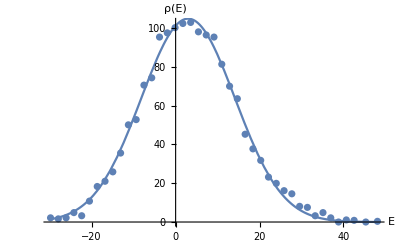

{{-62.7763,-30.4305,-1.5342},{-89.8324,-64.5241,-2.19386},{-97.2142,-73.5586,-2.37671},{-100.801,-90.9553,-3.24864},{-90.4794,-75.3582,-2.73776},{-112.835,-43.1149,-0.437388},{-179.164,-244.435,-6.63683},{-264.181,-351.977,-7.77649},{-2216.71,-1964.16,-55.8927},{-6696.08,-4641.87,-106.022},{-15310.4,-9923.39,-255.189}}

| Estimate | Standard Error | Confidence Interval
mu | 2.92741 | 0.201811 | {2.51089,3.34393}
sigma | 10.758 | 0.202075 | {10.3409,11.175}
Am | 0.994368 | 0.0161615 | {0.961012,1.02772}

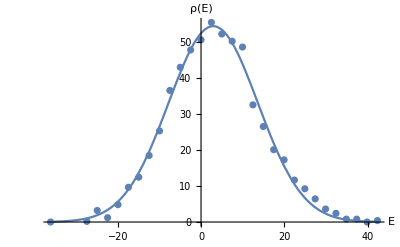

| Estimate | Standard Error | Confidence Interval
mu | 3.22578 | 0.393703 | {2.41797,4.03359}
sigma | 10.8427 | 0.396108 | {10.0299,11.6554}
Am | 1.00166 | 0.0315623 | {0.936897,1.06642}

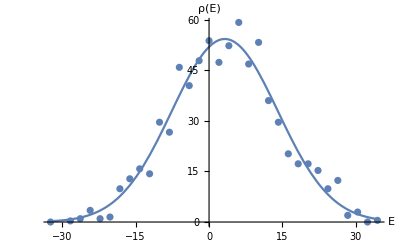

```mathematica
PlotEnergyBuckets[1,12,ColorN->12,Bucketed->42,PrintFit->True]
FindN2Correction[1,11,{11,20,21,22,25,30,40,50,100,200,300}]
PlotEnergyBuckets[1,11,GlobalFit->False,ColorN ->11,PrintFit->True]
PlotEnergyBuckets[1,11,GlobalFit->False,ColorN->21,PrintFit->True]
```

{{18,3.41811,13.3318,1.00289},{19,3.42213,13.6227,1.0025},{20,3.43047,13.9431,1.00295},{21,3.43463,14.2168,1.00259},{22,3.43683,14.4907,1.00237},{23,3.44396,14.7692,1.00235},{24,3.44855,15.0412,1.0023},{25,3.45252,15.3056,1.00221},{26,3.45506,15.566,1.00213},{27,3.45914,15.8248,1.00213},{28,3.46224,16.0781,1.0021},{29,3.4633,16.3259,1.00203},{30,3.46713,16.5717,1.00201},{31,3.46985,16.8133,1.00197}}

{b→3.55395,c→2.8128,d→6.36845}

{b→3.54229,c→2.25984}

{a→0.267028,b→8.59358}

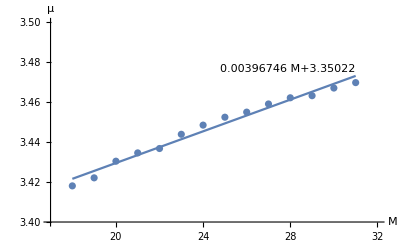

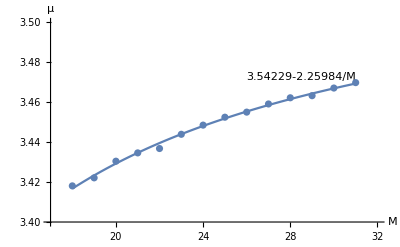

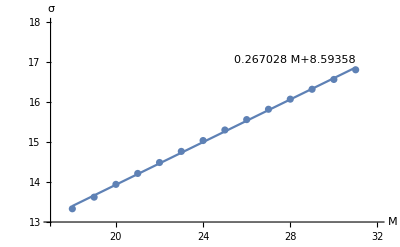

```mathematica
minM=18;
maxM = 31;
param=Table[Join[{m},FitEnergyData[1,m]],{m,minM,maxM}]
param1=param[[All,{1,2}]];
param2=param[[All,{1,3}]];
tfit1b=NonlinearModelFit[param1, a*M+b,{ b,a}, {M}];
tfit1=NonlinearModelFit[param1, b-c/M,{ b,c}, {M}];
tfit1c=NonlinearModelFit[param1, b-c/M+d/M^2,{ b,c,d}, {M}];
tfit2=NonlinearModelFit[param2, a*M+b,{a, b}, {M}];
tfit1c["BestFitParameters"]
tfit1["BestFitParameters"]
tfit2["BestFitParameters"]
SigmaFit[M_]:=tfit2[M];
MuFit[M_]:=tfit1[M];

tplot1=Plot[tfit1[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit1],Above],AxesLabel->{"M", "μ"},PlotRange->{{minM-1,maxM+1},{3.4,3.5}}];
tplot2=Plot[tfit2[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit2],Above],AxesLabel->{"M", "σ"},PlotRange->{{minM-1,maxM+1},{13,18}}];
tplot1b=Plot[tfit1b[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit1b],Above],AxesLabel->{"M", "μ"},PlotRange->{{minM-1,maxM+1},{3.4,3.5}}];
tplot1c=Plot[tfit1c[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit1c],Above],AxesLabel->{"M", "μ"},PlotRange->{{minM-1,maxM+1},{3.4,3.5}}];
s1=Show[tplot1b,ListPlot[param[[All,{1,2}]]]]
(*s1c=Show[tplot1c,ListPlot[param[[All,{1,2}]]]]*)
s2=Show[tplot1,ListPlot[param[[All,{1,2}]]]]
s3=Show[tplot2,ListPlot[param[[All,{1,3}]]]]
(*Export["mu.pdf",s1];
Export["fit-mu.pdf",s2];
Export["fit-sigma.pdf",s3];*)
Clear[s1,s2,s3,s1c]
```

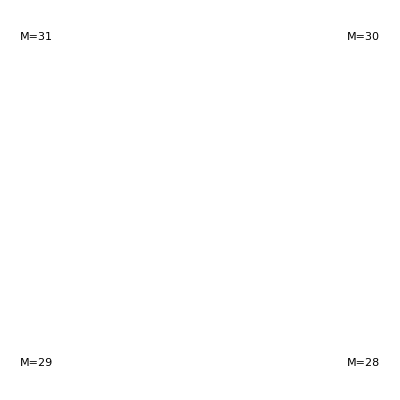

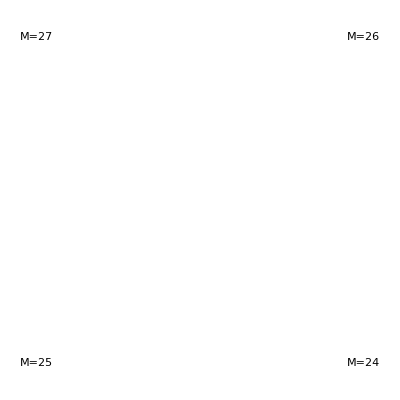

```mathematica
(*minM=19;
maxM=31;
For[ti=minM,ti≤maxM,ti++,
plot=Labeled[PlotEnergyBuckets[1,ti],"M="<>ToString[ti]];
Export["E-density-M"<>ToString[ti]<>".pdf",plot]
]
Clear[ti];*)
rescale=True;
g1=Labeled[PlotEnergyBuckets[1,31,NormScale->rescale],"M=31"];
g2=Labeled[PlotEnergyBuckets[1,30,NormScale->rescale],"M=30"];
g3=Labeled[PlotEnergyBuckets[1,29,NormScale->rescale],"M=29"];
g4=Labeled[PlotEnergyBuckets[1,28,NormScale->rescale],"M=28"];
GraphicsGrid[{{g1,g2},{g3,g4}}]

g1=Labeled[PlotEnergyBuckets[1,27,NormScale->rescale],"M=27"];
g2=Labeled[PlotEnergyBuckets[1,26,NormScale->rescale],"M=26"];
g3=Labeled[PlotEnergyBuckets[1,25,NormScale->rescale],"M=25"];
g4=Labeled[PlotEnergyBuckets[1,24,NormScale->rescale],"M=24"];
GraphicsGrid[{{g1,g2},{g3,g4}}]

ClearAll[g1,g2,g3,g4];
```

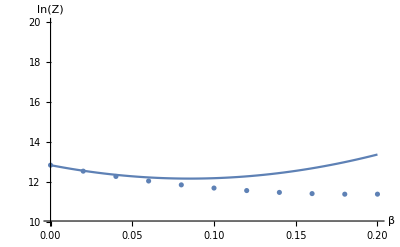

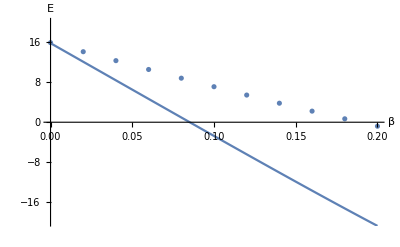

```mathematica
plots=PlotThermalData[1,19,1,0.2];
Show[plots[[1,1]],plots[[1,2]]]
Show[plots[[2,1]],plots[[2,2]]]
(*Show[plots[[3,1]]]
Show[plots[[4,1]]]*)
```

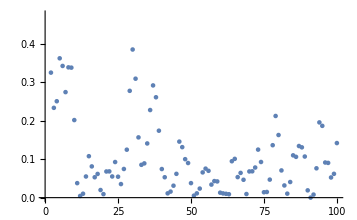

```mathematica
Show[PlotFluctuation[1,19]]
```

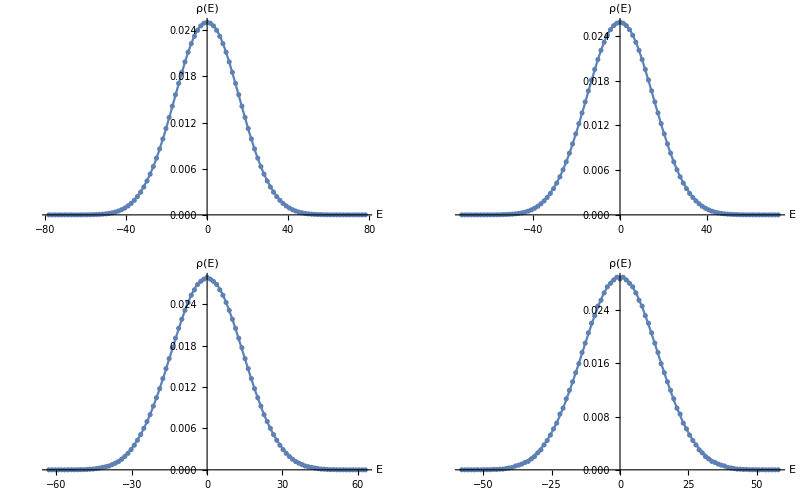

```mathematica
rescale=True;
g1=PlotEnergyBuckets[1,31,Single->True,NormScale->rescale];
g2=PlotEnergyBuckets[1,29,Single->True,NormScale->rescale];
g3=PlotEnergyBuckets[1,27,Single->True,NormScale->rescale];
g4=PlotEnergyBuckets[1,25,Single->True,NormScale->rescale];
g5=PlotEnergyBuckets[1,23,Single->True,NormScale->rescale];
g6=PlotEnergyBuckets[1,21,Single->True,NormScale->rescale];

GraphicsGrid[{{g1,g2},{g4,g5}}]
ClearAll[g1,g2,g3,g4,g5,g6];
```

{b→-0.000196684,c→-0.00407415}

{a→0.280089,b→7.32241}

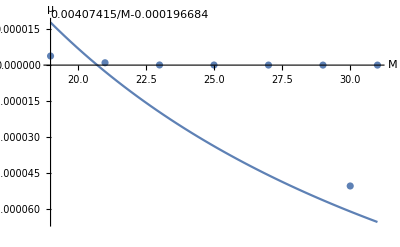

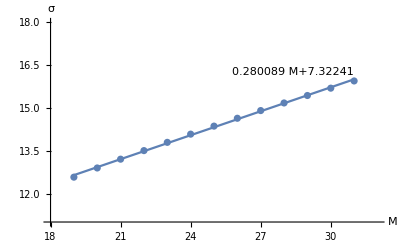

```mathematica
minM=19;
maxM = 31;
param=Table[Join[{m},FitEnergyData[1,m,Single->True]],{m,minM,maxM}];
param1=param[[All,{1,2}]];
param2=param[[All,{1,3}]];
tfit1=NonlinearModelFit[param1, b-c/M,{ b,c}, {M}];
tfit2=NonlinearModelFit[param2, a*M+b,{a, b}, {M}];

tfit1["BestFitParameters"]
tfit2["BestFitParameters"]

tplot1=Plot[tfit1[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit1],Above],AxesLabel->{"M", "μ"}];
tplot2=Plot[tfit2[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit2],Above],AxesLabel->{"M", "σ"},PlotRange->{{18,32},{11,18}}];
tplot1b=Plot[tfit1b[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit1b],Above],AxesLabel->{"M", "μ"}];

Show[tplot1,ListPlot[param[[All,{1,2}]]]]
(*Export["fit-mu.pdf",%];*)
Show[tplot2,ListPlot[param[[All,{1,3}]]]]
(*Export["fit-sigma-single.pdf",%];*)
```